#### bin

```mathematica
AbsoluteTiming[
values=If[Head@Values[bin]===Association,First[Values[bin]],Values[bin]];
{ethV,exV,volV}=Transpose[{{#1,#2},{#1,#3},{#1,#5}}&@@@values];
{ethTS,exTS,volTS}=TimeSeries/@{ethV,exV,volV};
btcTS=ethTS/exTS;]
```

{10.9302,Null}

```mathematica
{firstTick,firstVal}=First@ethV
{lastTick,lastVal}=Last@ethV
```

{{2017,8,18,0,31,7.61},305.535}

{{2017,12,11,9,4,16.},474.7}

```mathematica
Now
DateDifference[Now,lastTick,"Minutes"]
```

Mon 11 Dec 2017 08:12:19GMT-6.

51.9393 min

DataDrop ticker is on -5 GMT. This was masked by Daylight Savings.

#### charts

```mathematica
windowHours=4;
```

```mathematica
q=MovingMap[
Quantile[#,{1/10,1/2,9/10},{{1/2,0},{0,1}}]&,
exTS,
Quantity[Round[windowHours*12],"Events"]];
{q10,q50,q90}=
{q["PathComponent",1],q["PathComponent",2],q["PathComponent",3]};
windowedGain=(2 e s sd)/(2 m+sd)/.{e->ethTS,m->q50,sd->q90-q10,s->10};
rates=Join[q["LastValue"],{exTS["LastValue"]}];
```

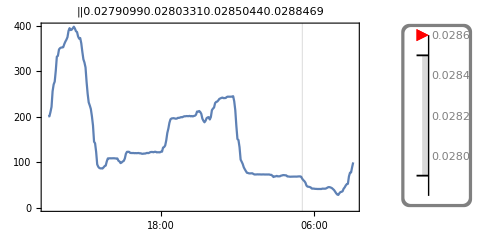

```mathematica
With[{
start=DatePlus[lastTick,-Quantity[1,"Days"]],
window=DatePlus[lastTick,-Quantity[windowHours,"Hours"]]},
GraphicsRow[{
DateListPlot[
TimeSeriesWindow[windowedGain,{start,lastTick}],
Joined->True,
PlotLabel->Row[rates,"|"],
ImageSize->300,
PlotRange->{{start,All},All},
GridLines->{{window},None}],
rateGuage[rates]},ImageSize->480,Spacings->-100]]
```

Hours of history of coinmarketcap ETH/BTC exchange, not the same as GDAX

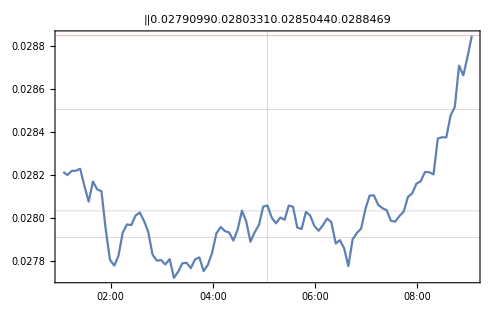

```mathematica
With[{
start=DatePlus[lastTick,-Quantity[2*windowHours,"Hours"]],
window=DatePlus[lastTick,-Quantity[windowHours,"Hours"]]},
DateListPlot[
TimeSeriesWindow[exTS,{start,lastTick}],
Joined->True,
GridLines->{{window},MapAt[{#,Directive[Red,Thick]}&,rates,4]},
PlotLabel->Row[rates,"|"],
ImageSize->500,
PlotRange->{{start,All},Automatic}]]
```

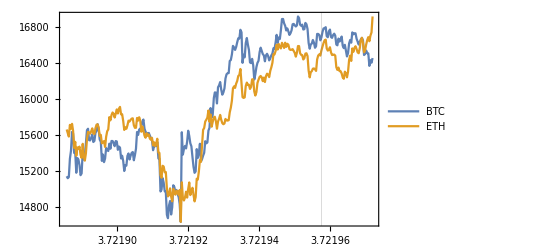

```mathematica
With[{
start=DatePlus[lastTick,-Quantity[1,"Days"]],
window=DatePlus[lastTick,-Quantity[windowHours,"Hours"]]},
 TwoAxisDateListPlot[
  Normal[TimeSeriesWindow[btcTS, {start, lastTick}]],
  Normal[TimeSeriesWindow[ethTS, {start, lastTick}]],
  PlotLegends -> {"BTC", "ETH"},
  PlotLabel -> "",
  PlotRange -> {{start, All}, All},
GridLines->{{window},None}]]
```

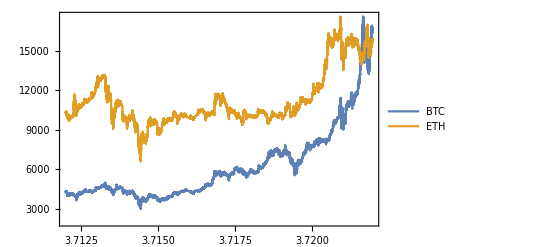

```mathematica
TwoAxisDateListPlot[
    Normal[btcTS],
    Normal[ethTS],
    PlotLegends -> {"BTC", "ETH"},
    PlotLabel -> "",
    PlotRange -> {{firstTick, All}, {2000, Automatic}}]
```

Quartiles[list] is equivalent to Quantile[list,{1/4,1/2,3/4},{{1/2,0},{0,1}}]

```mathematica
btceth=Transpose@Map[Last,Map[Normal,{btcTS,ethTS},1],{2}];
```

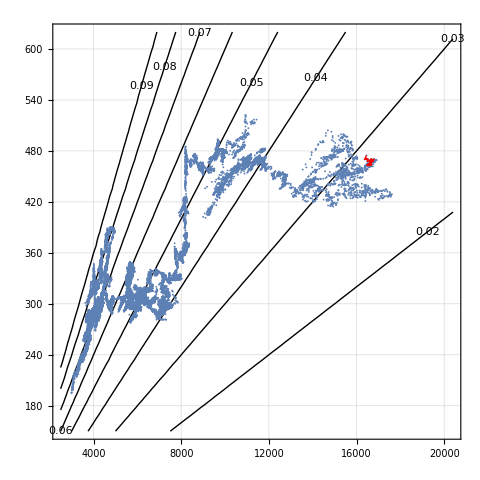

```mathematica
scatterplot=Show[
rateLevels,
ListPlot[btceth,PlotTheme->"Detailed",PlotRange->All],
Graphics[{Red,Line[Take[btceth,-windowHours*12]]}],
AspectRatio->1,GridLines->Automatic,ImageSize->480]
```

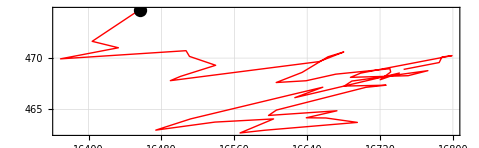

```mathematica
Show[Graphics[{
Red,Line[Take[btceth,-windowHours*12]],
Black,PointSize[.02],Point[Take[btceth,-1]]}],
AspectRatio->1/(2 GoldenRatio),Frame->True,GridLines->Automatic]
```

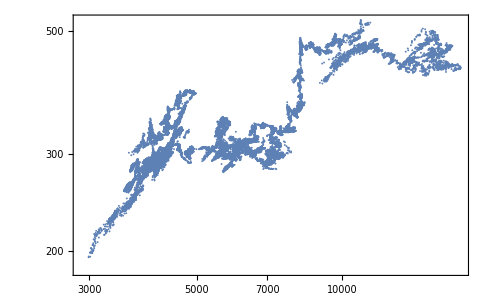

```mathematica
ListLogLogPlot[btceth,PlotTheme->"Detailed",PlotRange->All]
```

#### returns

Return is the (5 min. step) change in the Log of the Price

```mathematica
btcethReturns=btceth//RightComposition[
Transpose,
Log[Drop[#,1]]-Log[Drop[#,-1]]&/@#&,
Transpose
];
```

```mathematica
tsReturns=TemporalData[Transpose[btcethReturns],
{Automatic,lastTick,Quantity[5,"Minutes"]}];
```

```mathematica
tsReturns5d=TimeSeriesWindow[tsReturns, {DatePlus[lastTick,-Quantity[5,"Days"]], lastTick}];
```

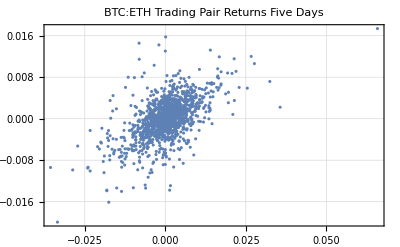

```mathematica
ListPlot[Transpose@tsReturns5d["ValueList"],
PlotLabel->"BTC:ETH Trading Pair Returns Five Days",
PlotTheme->"Detailed",PlotRange->All]
```

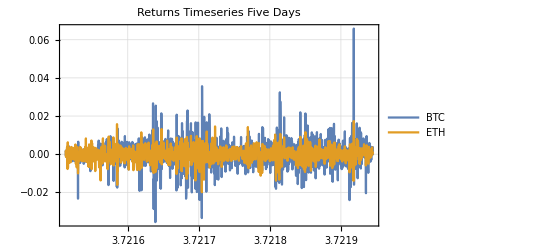

```mathematica
DateListPlot[tsReturns5d,
PlotLegends->{"BTC","ETH"},
PlotLabel->"Returns Timeseries Five Days",
PlotTheme->"Detailed",PlotRange->All]
```

```mathematica
btcethValue5d=tsReturns5d["ValueList"]//
RightComposition[
FoldList[Times,1000,ⅇ^#]&/@#&,
Transpose
];
```

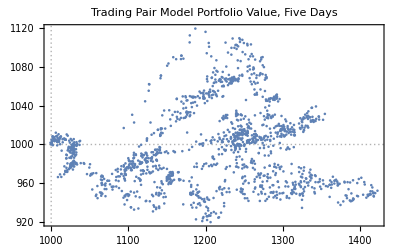

```mathematica
ListPlot[btcethValue5d,
PlotLabel->"Trading Pair Model Portfolio Value, Five Days",
PlotTheme->"Detailed",PlotRange->All,
GridLines->{{1000},{1000}}]
```

```mathematica
tsValue5d=TemporalData[Transpose[btcethValue5d],
{Automatic,lastTick,Quantity[5,"Minutes"]}];
```

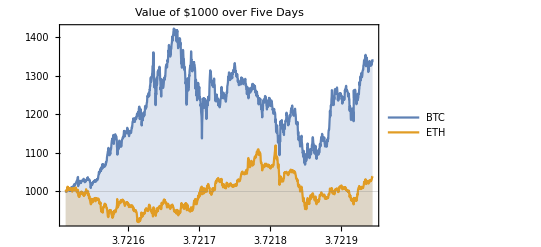

```mathematica
DateListPlot[tsValue5d,
Filling->Axis,PlotLabel->"Value of $1000 over Five Days",
PlotRange->All,PlotLegends->{"BTC","ETH"},
GridLines->{None,{1000}}]
```

```mathematica
tsValue5d["FirstDate"]
```

Wed 6 Dec 2017 01:24:16GMT-6.

#### code

```mathematica
bin=Databin["nZWjPQuw"]
```

Databin[…]

```mathematica
rateGuage[{lq_,med_,uq_,rt_}]:=Module[{},
VerticalGauge[{rt,lq,uq,rt},{lq,uq}+{-1,1}*.0001,
GaugeMarkers->{"Marker","BarMarker","BarMarker"},
GaugeStyle->{Red,Black,Black},
GaugeFrameStyle->Gray,
ScalePadding->{.20,.05},
ScaleOrigin->-.05,
ScaleRanges->{{lq,uq}->LightGray}]]
```

```mathematica
TwoAxisDateListPlot[f_List,g_List,opts:OptionsPattern[]]:=Module[
{p1,p2,fm,fM,gm,gM,old(*,new,newg*)},
p1=DateListPlot[f,Axes->True,Frame->False,PlotRange->Automatic];
p2=DateListPlot[g,Axes->True,Frame->False,PlotRange->Automatic];
{fm,fM}=AbsoluteOptions[p1,PlotRange][[1,2,2]];
{gm,gM}=AbsoluteOptions[p2,PlotRange][[1,2,2]];
old=AbsoluteOptions[p2,Ticks][[1,2,2]];
new=Flatten[{Rescale[First[#1],{gm,gM},{fm,fM}],Rest[#1]},1]&/@old;
newg={#[[1]],Rescale[#[[2]],{gm,gM},{fm,fM}]}&/@g;
DateListPlot[{f,newg},
Axes->False,Frame->True,
FrameTicks->{{Automatic,new},{Automatic,Automatic}},
opts,PlotRange->{fm,fM},opts]]
```

Flatten[{Rescale[First[#1], {fm, fM}, {gm, gM}], Rest[#1]}, 1
] & /@ Sort@AbsoluteOptions[p1, Ticks][[1, 2, 2]]

```mathematica
rateLevels=ContourPlot[e1/b1,
{b1,2500,20400},{e1,150,620},
Contours->{.020,.030,.040,.050,.060,.070,.080,.090},
ContourShading->None,
ContourLabels->(Text[#3,{#1,#2},Background->LightGray]&),
ColorFunctionScaling->True];
```